```mathematica
bullseye[μ_,σ_,n_,]:=Show[ListPlot[RandomVariate[MultinormalDistribution[μ,σ{{1,0},{0,1}}]//Evaluate,n],PlotRange->{{-2.1,2.1},{-2.1,2.1}},AspectRatio->1,PlotMarkers->{Automatic,Medium},Axes->None],
ParametricPlot[Table[r{Cos[θ],Sin[θ]},{r,0,2,1/2}],{θ,0,2π}]]
```

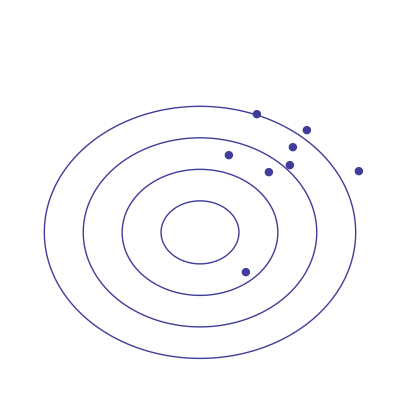
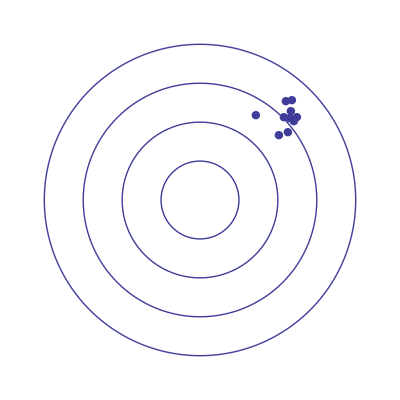
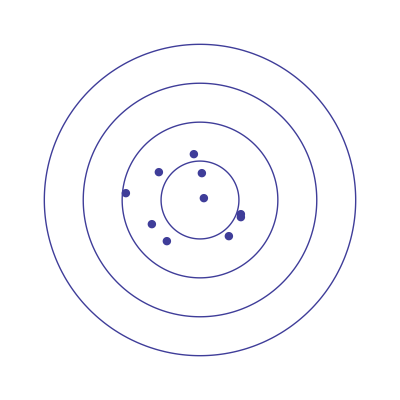
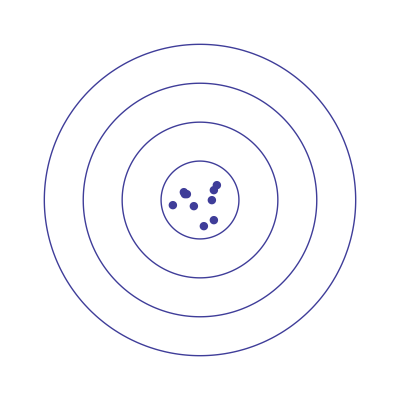
| Imprecise | Precise
Inaccurate | -Graphics- | -Graphics-
Accurate | -Graphics- | -Graphics-

```mathematica
Grid[{{"","Imprecise","Precise"},
{"Inaccurate",bullseye[{1,1},.5,10],bullseye[{1,1},.025,10]},{"Accurate",bullseye[{0,0},.5,10],bullseye[{0,0},.025,10]}},Frame->All]
```

```mathematica
Export["C:\\Users\\Michael\\Pictures\\accuracy-vs-precision.png",%48]
```

C:\Users\Michael\Pictures\accuracy-vs-precision.png

```mathematica
SystemOpen["C:\\Users\\Michael\\Pictures\\accuracy-vs-precision.png"]
```